```mathematica
ClearAll[d0,d1,ω,ν,η,η1,η2,d,l]
```

```mathematica
Do[

Do[

(*For[d=0.08,d<0.081,d+=0.0002,*)

dd=ToString[d];
ll=ToString[l];
v="9";
p="0.1";
frt=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/BreakJam2/Fourier1D-d"<>dd<>"-l"<>ll<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];

frts[l][d]=Table[frt[[i]],{i,1,Length[frt]/(10)}];

frf=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/BreakJam2/Fourier1DFree-d"<>dd<>"-l"<>ll<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];

frfs[l][d]=Table[frf[[i]],{i,1,Length[frf]/(10)}];

frbaux=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/BreakJam2/Fourier1DBreak-d"<>dd<>"-l"<>ll<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];

frb=Table[frbaux[[i]],{i,1,Length[frbaux],2}];

frbs[l][d]=Table[frb[[i]],{i,1,Length[frb]/(10)}];


,{d,{0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898}}]

(*,{l,{5,10,20,30,40,50}}]*)
,{l,{5,10,20,30}}]
```

```mathematica
vmax=9;
d0=0.0812;
df=0.081;
d1=0.105;
ω=0.3825;
ν=1/0.13;
η1[l_]:=((((-df+d0+d1*(l*1000)^(-ω))/d0)^ν)*vmax);
η11[l_]:=((((-df+d0)/d0)^ν)*vmax);
η2[l_]:=η1[l]/(1000*l);
η22[l_]:=η11[l]/(1000*l);
(*η1=0.0001;
η2=0.0001;*)




ξ[l_][d_]:=(η1[l])/(Abs[(d-d0-d1*(l*1000)^(-ω))/d0]^ν+η2[l])
ξ1[l_][d_]:=Abs[(d-d0-d1*(l*1000)^(-ω))/d0]^(-ν)
ξaux[l_][d_]:=(η1[l])/(Abs[(d-d0-d1*(l*1000)^(-ω))/d0]^ν)
```

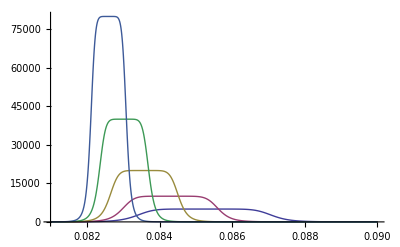

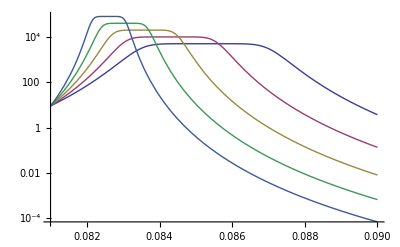

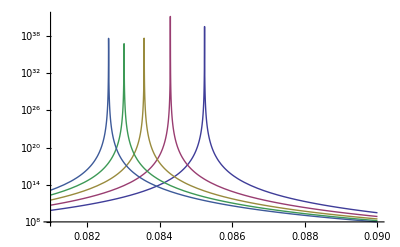

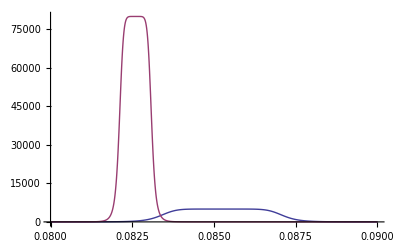

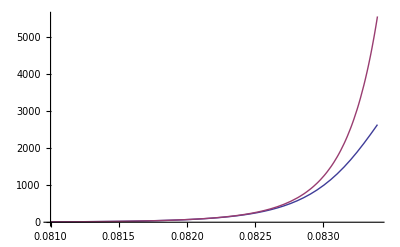

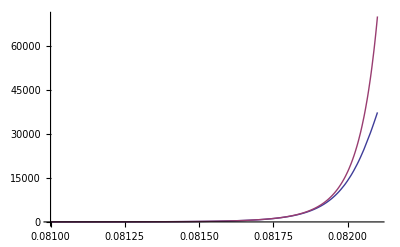

```mathematica
Plot[{ξ[5][x],ξ[10][x],ξ[20][x],ξ[40][x],ξ[80][x]},{x,0.081,0.09},PlotRange->Full]
LogPlot[{ξ[5][x],ξ[10][x],ξ[20][x],ξ[40][x],ξ[80][x]},{x,0.081,0.09},PlotRange->Full]
LogPlot[{ξ1[5][x],ξ1[10][x],ξ1[20][x],ξ1[40][x],ξ1[80][x]},{x,0.081,0.09},PlotRange->Full]
Plot[{ξ[5][x],ξ[80][x]},{x,0.08,0.09},PlotRange->Full]
Plot[{ξ[5][x],ξaux[5][x]},{x,0.081,0.0834},PlotRange->Full]
Plot[{ξ[80][x],ξaux[80][x]},{x,0.081,0.0821},PlotRange->Full]
```

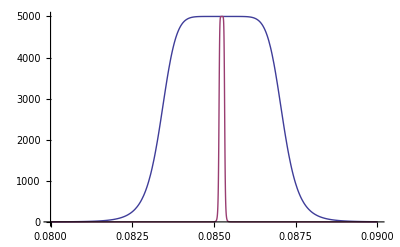

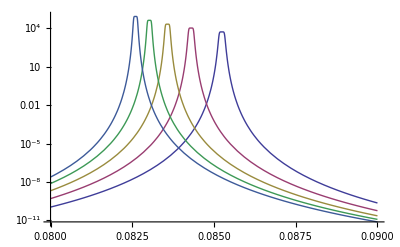

```mathematica
Plot[{ξ[5][x],ξ1[5][x]},{x,0.08,0.09},PlotRange->Full]
LogPlot[{ξ1[5][x],ξ1[10][x],ξ1[20][x],ξ1[40][x],ξ1[80][x]},{x,0.08,0.09},PlotRange->Full]
```

```mathematica
Do[
Do[

frbss[l][d]=Table[{frbs[l][d][[All,1]][[i]]*π/(l*1000.)*ξ[l][d],frbs[l][d][[All,2]][[i]]},{i,1,Length[frbs[l][d]]}];

frbss1[l][d]=Table[{frbs[l][d][[All,1]][[i]]*π/(l*1000.)*ξ1[l][d],frbs[l][d][[All,2]][[i]]},{i,1,Length[frbs[l][d]]}];

,{d,{0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898}}
]
,{l,{5,10,20,30,40,50}}]
```

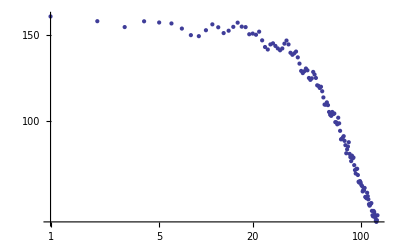

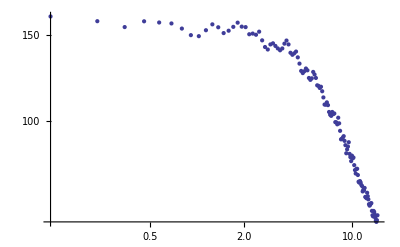

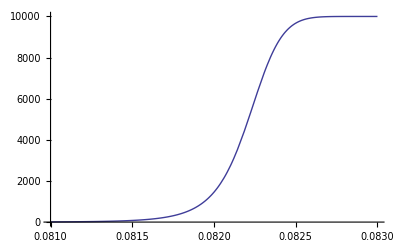

```mathematica
ListLogLogPlot[frbs[40][0.082]]
ListLogLogPlot[frbss[40][0.082]]
Plot[{ξ[40][x]},{x,0.081,0.083},PlotRange->Full]
```

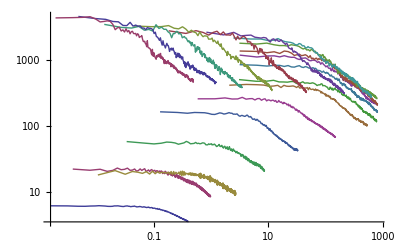

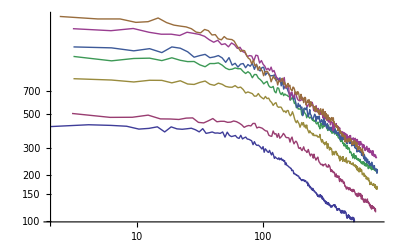

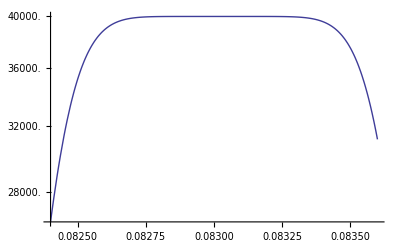

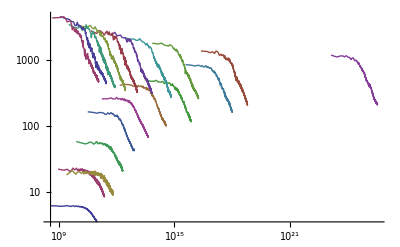

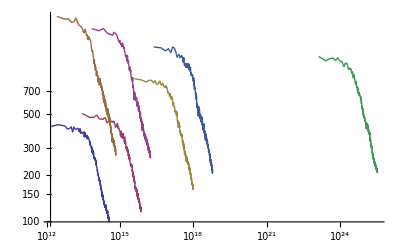

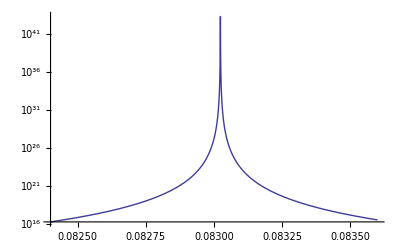

```mathematica
ListLogLogPlot[{frbss[40][0.0812],frbss[40][0.0814],frbss[40][0.0816],frbss[40][0.0818],frbss[40][0.082],frbss[40][0.0822],frbss[40][0.0824],frbss[40][0.0826],frbss[40][0.0828],frbss[40][0.083],frbss[40][0.0832],frbss[40][0.0834],frbss[40][0.0836],frbss[40][0.0838],frbss[40][0.084],frbss[40][0.0842],frbss[40][0.0844],frbss[40][0.0846],frbss[40][0.0848]},PlotRange->Full,Joined->True]
ListLogLogPlot[{frbss[40][0.0824],frbss[40][0.0826],frbss[40][0.0828],frbss[40][0.083],frbss[40][0.0832],frbss[40][0.0834],frbss[40][0.0836]},PlotRange->Full,Joined->True]
LogPlot[ξ[40][d],{d,0.0824,0.0836},PlotRange->Full]
ListLogLogPlot[{frbss1[40][0.0812],frbss1[40][0.0814],frbss1[40][0.0816],frbss1[40][0.0818],frbss1[40][0.082],frbss1[40][0.0822],frbss1[40][0.0824],frbss1[40][0.0826],frbss1[40][0.0828],frbss1[40][0.083],frbss1[40][0.0832],frbss1[40][0.0834],frbss1[40][0.0836],frbss1[40][0.0838],frbss1[40][0.084],frbss1[40][0.0842],frbss1[40][0.0844],frbss1[40][0.0846],frbss1[40][0.0848]},PlotRange->Full,Joined->True]
ListLogLogPlot[{frbss1[40][0.0824],frbss1[40][0.0826],frbss1[40][0.0828],frbss1[40][0.083],frbss1[40][0.0832],frbss1[40][0.0834],frbss1[40][0.0836]},PlotRange->Full,Joined->True]
LogPlot[ξ1[40][d],{d,0.0824,0.0836},PlotRange->Full]
```

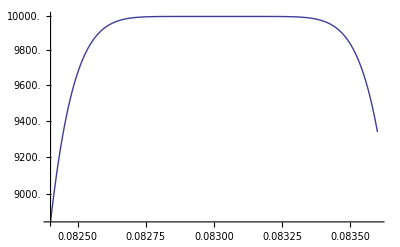

```mathematica
LogPlot[ξ[40][d],{d,0.0824,0.0836},PlotRange->Full]
```

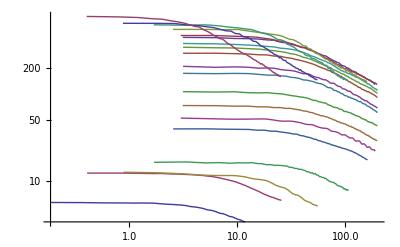

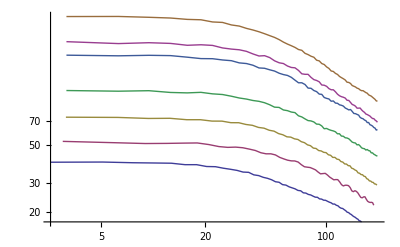

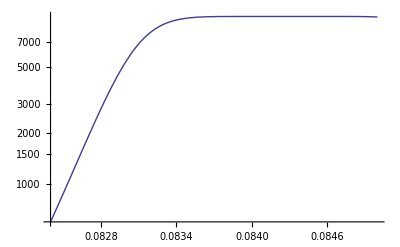

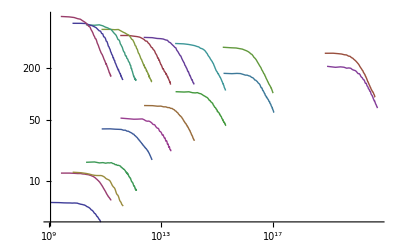

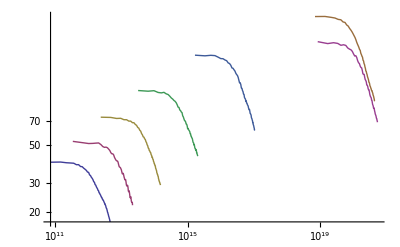

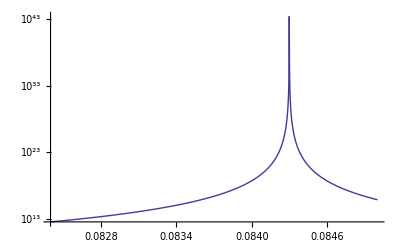

```mathematica
ListLogLogPlot[{frbss[10][0.0824],frbss[10][0.0826],frbss[10][0.0828],frbss[10][0.083],frbss[10][0.0832],frbss[10][0.0834],frbss[10][0.0836],frbss[10][0.0838],frbss[10][0.084],frbss[10][0.0842],frbss[10][0.0844],frbss[10][0.0846],frbss[10][0.0848],frbss[10][0.085],frbss[10][0.0852],frbss[10][0.0854],frbss[10][0.0856],frbss[10][0.0858],frbss[10][0.086]},PlotRange->Full,Joined->True]
ListLogLogPlot[{frbss[10][0.0832],frbss[10][0.0834],frbss[10][0.0836],frbss[10][0.0838],frbss[10][0.084],frbss[10][0.0842],frbss[10][0.0844]},PlotRange->Full,Joined->True]
LogPlot[ξ[10][d],{d,0.0824,0.085},PlotRange->Full]
ListLogLogPlot[{frbss1[10][0.0824],frbss1[10][0.0826],frbss1[10][0.0828],frbss1[10][0.083],frbss1[10][0.0832],frbss1[10][0.0834],frbss1[10][0.0836],frbss1[10][0.0838],frbss1[10][0.084],frbss1[10][0.0842],frbss1[10][0.0844],frbss1[10][0.0846],frbss1[10][0.0848],frbss1[10][0.085],frbss1[10][0.0852],frbss1[10][0.0854],frbss1[10][0.0856],frbss1[10][0.0858],frbss1[10][0.086]},PlotRange->Full,Joined->True]
ListLogLogPlot[{frbss1[10][0.0832],frbss1[10][0.0834],frbss1[10][0.0836],frbss1[10][0.0838],frbss1[10][0.084],frbss1[10][0.0842],frbss1[10][0.0844]},PlotRange->Full,Joined->True]
LogPlot[ξ1[10][d],{d,0.0824,0.085},PlotRange->Full]
```

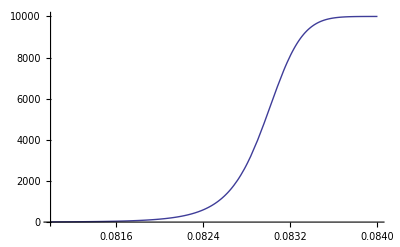

```mathematica
Plot[ξ[10][d],{d,0.081,0.084},PlotRange->Full]
```

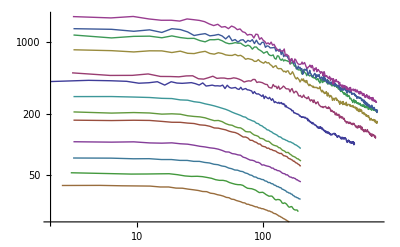

```mathematica
ListLogLogPlot[{frbss[40][0.0824],frbss[40][0.0826],frbss[40][0.0828],frbss[40][0.083],frbss[40][0.0832],frbss[40][0.0834],frbss[10][0.0832],frbss[10][0.0834],frbss[10][0.0836],frbss[10][0.0838],frbss[10][0.084],frbss[10][0.0842],frbss[10][0.0844]},PlotRange->Full,Joined->True]
```

```mathematica
ListLogLogPlot[{frbss[40][0.0824],frbss[40][0.0826],frbss[40][0.0828],frbss[40][0.083],frbss[40][0.0832],frbss[10][0.0832],frbss[10][0.0834],frbss[10][0.0836],frbss[10][0.0838],frbss[10][0.084],frbss[10][0.0842],frbss[10][0.0844]},PlotRange->Full,Joined->True]
LogPlot[{ξ[10][d],ξ[40][d]},{d,0.081,0.084},PlotRange->Full]
```

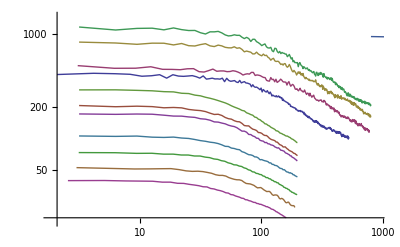

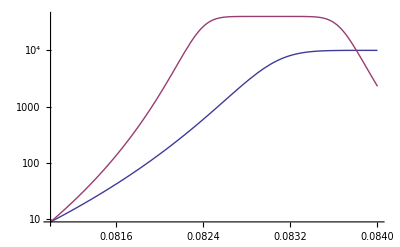

```mathematica
ListLogLogPlot[{frbss1[40][0.0824],frbss1[40][0.0826],frbss1[40][0.0828],frbss1[40][0.083],frbss1[40][0.0832],frbss1[40][0.0834],frbss1[10][0.0832],frbss1[10][0.0834],frbss1[10][0.0836],frbss1[10][0.0838],frbss1[10][0.084],frbss1[10][0.0842],frbss1[10][0.0844]},PlotRange->Full,Joined->True]
```

```mathematica
Do[
maxft[l]=Table[{d,frts[l][d][[1]][[2]]},{d,{0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898}}];

maxft2[l]=Table[{d,frts[l][d][[1]][[2]]/(l*1000*d)^2},{d,{0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898}}];

maxff[l]=Table[{d,frfs[l][d][[1]][[2]]},{d,{0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898}}];

maxff2[l]=Table[{d,frfs[l][d][[1]][[2]]/(l*1000*d)^2},{d,{0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898}}];


maxfb[l]=Table[{d,frbs[l][d][[1]][[2]]},{d,{0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898}}];

maxfb2[l]=Table[{d,frbs[l][d][[1]][[2]]/(l*1000*d)^2},{d,{0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898}}];


η=0;
maxfb2s[l]=Table[{(d-(d0+1*(l*1000)^(-ω)))*(l*1000)^(-1/ν),frbs[l][d][[1]][[2]]*(l*1000*d)^(η-2)},{d,{0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898}}];

,{l,{5,10,20,30,40,50}}]
```

```mathematica
η1[l_]:=((((-df+d0+d1*(l*1000)^(-ω))/d0)^ν)*vmax)
```

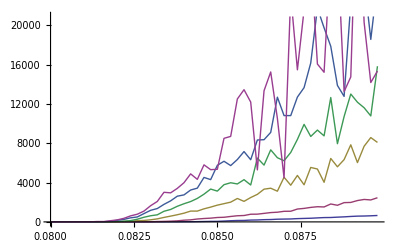

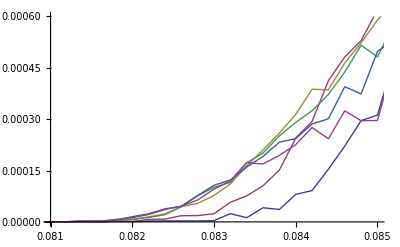

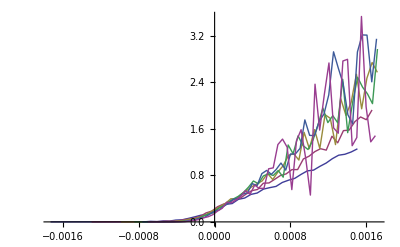

```mathematica
ListLinePlot[{maxfb[5],maxfb[10],maxfb[20],maxfb[30],maxfb[40],maxfb[50]}]
ListLinePlot[{maxfb2[5],maxfb2[10],maxfb2[20],maxfb2[30],maxfb2[40],maxfb2[50]},PlotRange->{{0.081,0.085},{0,0.0006}}]
ListLinePlot[{maxfb2s[5],maxfb2s[10],maxfb2s[20],maxfb2s[30],maxfb2s[40],maxfb2s[50]},PlotRange->Full]
```

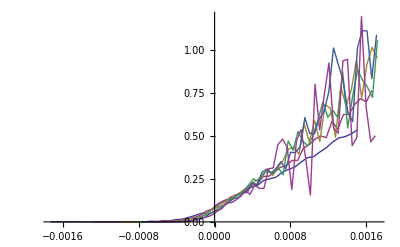

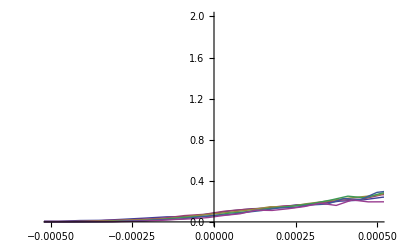

```mathematica
Do[
η=0.6;
maxfb2s[l]=Table[{(d-(d0+d1*(l*1000)^(-ω)))*(l*1000)^(-1/ν),frbs[l][d][[1]][[2]]*d^(-2)*(l*1000)^(η-2)},{d,{0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898}}];

,{l,{5,10,20,30,40,50}}]

ListPlot[{maxfb2s[5],maxfb2s[10],maxfb2s[20],maxfb2s[30],maxfb2s[40],maxfb2s[50]},PlotRange->Full,Joined->True]
ListLinePlot[{maxfb2s[5],maxfb2s[10],maxfb2s[20],maxfb2s[30],maxfb2s[40],maxfb2s[50]},PlotRange->{{-0.0005,0.0005},{0,2}}]
```

```mathematica
Do[

Do[

(*For[d=0.08,d<0.081,d+=0.0002,*)

dd=ToString[d];
ll=ToString[l];
v="9";
p="0.1";
frt=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/BreakJam2/Fourier1D-d"<>dd<>"-l"<>ll<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];

frts[l][d]=Table[frt[[i]],{i,1,Length[frt]/(Pi*50)}];

frf=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/BreakJam2/Fourier1DFree-d"<>dd<>"-l"<>ll<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];

frfs[l][d]=Table[frf[[i]],{i,1,Length[frf]/(Pi*50)}];

frbaux=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/BreakJam2/Fourier1DBreak-d"<>dd<>"-l"<>ll<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];

frb=Table[frbaux[[i]],{i,1,Length[frbaux],2}];

frbs[l][d]=Table[frb[[i]],{i,1,Length[frb]/(Pi*50)}];


,{d,{0.084}}]
,{l,{5}}]
```

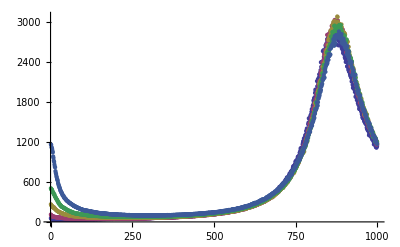

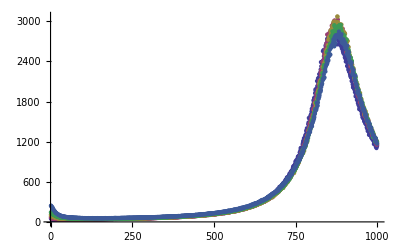

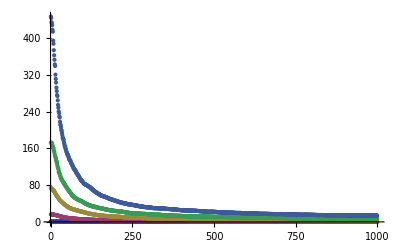

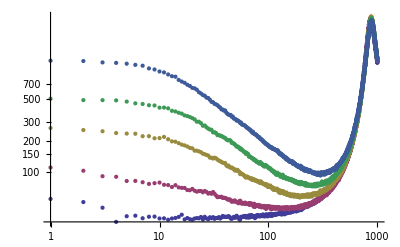

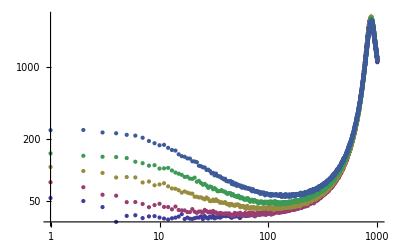

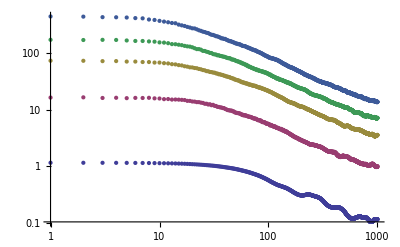

```mathematica
l=10;
d1=0.082;
d2=0.083;
d3=0.0836;
d4=0.084;
d5=0.085;
ListPlot[{frts[l][d1],frts[l][d2],frts[l][d3],frts[l][d4],frts[l][d5]},PlotRange->{{0,1000},Full}]
ListPlot[{frfs[l][d1],frfs[l][d2],frfs[l][d3],frfs[l][d4],frfs[l][d5]},PlotRange->{{0,1000},Full}]
ListPlot[{frbs[l][d1],frbs[l][d2],frbs[l][d3],frbs[l][d4],frbs[l][d5]},PlotRange->{{0,1000},Full}]
ListLogLogPlot[{frts[l][d1],frts[l][d2],frts[l][d3],frts[l][d4],frts[l][d5]},PlotRange->{{1,1000},Full}]
ListLogLogPlot[{frfs[l][d1],frfs[l][d2],frfs[l][d3],frfs[l][d4],frfs[l][d5]},PlotRange->{{1,1000},Full}]
ListLogLogPlot[{frbs[l][d1],frbs[l][d2],frbs[l][d3],frbs[l][d4],frbs[l][d5]},PlotRange->{{1,1000},Full}]
```

```mathematica
ListLogLogPlot[{frbs[l][d1],frbs[l][d2],frbs[l][d3],frbs[l][d4],frbs[l][d5]},PlotRange->{{1,1000},Full}]
```

-Graphics-

```mathematica
i[d1]=Interpolation[frbs[l][d1]];
```

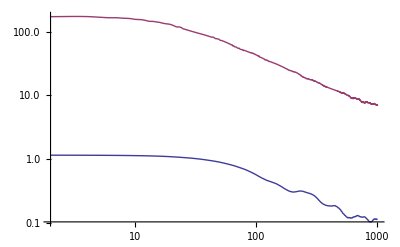

```mathematica
LogLogPlot[{i[d1][x],i[d4][x]},{x,2,1000}]
```

```mathematica
v=NSolve[i[d1][x]==0.5,x];
```

```mathematica
aux=((frbs[l][d4][[1]][[2]]+frbs[l][d4][[2]][[2]]+frbs[l][d4][[3]][[2]]+frbs[l][d4][[4]][[2]]+frbs[l][d4][[5]][[2]])/5)/2
```

85.6382

```mathematica
d=0.085
Select[frbs[l][d],((frbs[l][d][[1]][[2]]+frbs[l][d][[2]][[2]]+frbs[l][d][[3]][[2]]+frbs[l][d][[4]][[2]]+frbs[l][d][[5]][[2]])/5)/2 > #[[2]] &][[1]][[1]]
```

0.085

29

```mathematica
l=10;
turn[l]=Table[{d,Select[frbs[l][d],((frbs[l][d][[1]][[2]]+frbs[l][d][[2]][[2]]+frbs[l][d][[3]][[2]]+frbs[l][d][[4]][[2]]+frbs[l][d][[5]][[2]])/5)/2 > #[[2]] &][[1]][[1]]},{d,{0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898}}]
```

{{0.08,705},{0.0802,279},{0.0804,123},{0.0806,216},{0.0808,155},{0.081,84},{0.0812,143},{0.0814,78},{0.0816,159},{0.0818,134},{0.082,99},{0.0822,56},{0.0824,87},{0.0826,59},{0.0828,47},{0.083,57},{0.0832,54},{0.0834,52},{0.0836,46},{0.0838,45},{0.084,41},{0.0842,37},{0.0844,33},{0.0846,32},{0.0848,30},{0.085,29},{0.0852,27},{0.0854,24},{0.0856,23},{0.0858,23},{0.086,21},{0.0862,23},{0.0864,20},{0.0866,19},{0.0868,17},{0.087,18},{0.0872,17},{0.0874,16},{0.0876,15},{0.0878,15},{0.088,13},{0.0882,15},{0.0884,13},{0.0886,14},{0.0888,13},{0.089,14},{0.0892,13},{0.0894,11},{0.0896,12},{0.0898,11}}

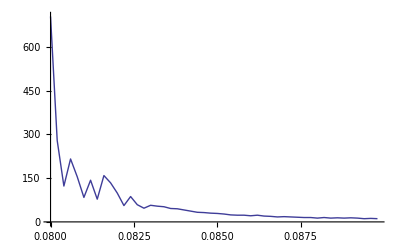

```mathematica
ListLinePlot[{turn[10]},PlotRange->Full]
```

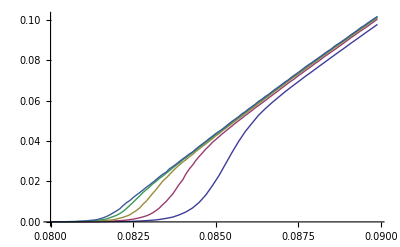

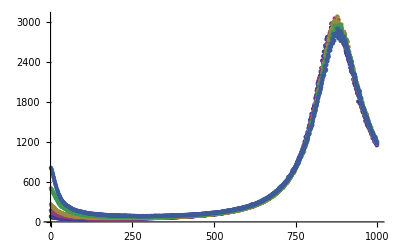

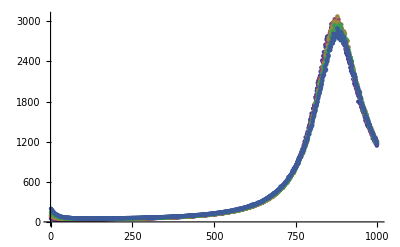

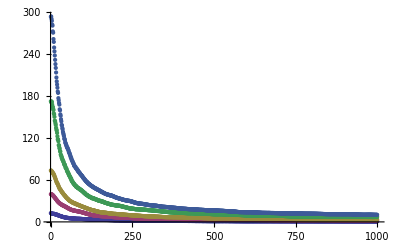

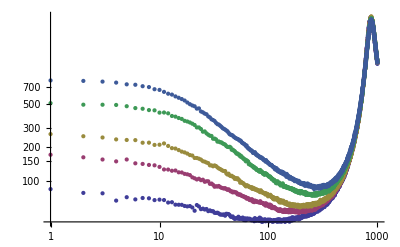

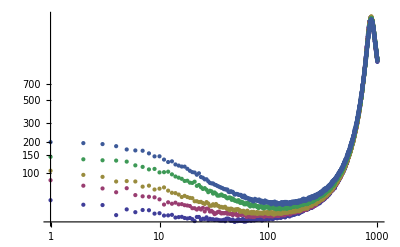

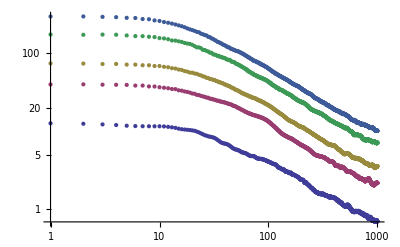

```mathematica
l=10;
d1=0.0828;
d2=0.0832;
d3=0.0836;
d4=0.084;
d5=0.0844;
ListPlot[{frts[l][d1],frts[l][d2],frts[l][d3],frts[l][d4],frts[l][d5]},PlotRange->{{0,1000},Full}]
ListPlot[{frfs[l][d1],frfs[l][d2],frfs[l][d3],frfs[l][d4],frfs[l][d5]},PlotRange->{{0,1000},Full}]
ListPlot[{frbs[l][d1],frbs[l][d2],frbs[l][d3],frbs[l][d4],frbs[l][d5]},PlotRange->{{0,1000},Full}]
ListLogLogPlot[{frts[l][d1],frts[l][d2],frts[l][d3],frts[l][d4],frts[l][d5]},PlotRange->{{1,1000},Full}]
ListLogLogPlot[{frfs[l][d1],frfs[l][d2],frfs[l][d3],frfs[l][d4],frfs[l][d5]},PlotRange->{{1,1000},Full}]
ListLogLogPlot[{frbs[l][d1],frbs[l][d2],frbs[l][d3],frbs[l][d4],frbs[l][d5]},PlotRange->{{1,1000},Full}]
```

```mathematica
l=10;
d=0.08;
frts[l][d][[1]][[2]]
```

0.08⟦2⟧

```mathematica
Do[

Do[

frtslog[l][d]=Table[{Log[frts[l][d][[i]][[1]]*π/l],Log[frts[l][d][[i]][[2]]]},{i,1,Length[frts[l][d]]}];

frfslog[l][d]=Table[{Log[frfs[l][d][[i]][[1]]*π/l],Log[frfs[l][d][[i]][[2]]]},{i,1,Length[frfs[l][d]]}];

frbslog[l][d]=Table[{Log[frbs[l][d][[i]][[1]]*π/l],Log[frbs[l][d][[i]][[2]]]},{i,1,Length[frbs[l][d]]}];


,{d,{0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898}}]


(*,{l,{5,10,20,30,40,50}}]*)
,{l,{5,10,20,30}}]
```

```mathematica
Do[
turn[l]=Table[{d,Select[frbslog[l][d],((frbslog[l][d][[1]][[2]]+frbslog[l][d][[2]][[2]]+frbslog[l][d][[3]][[2]]+frbslog[l][d][[4]][[2]]+frbslog[l][d][[5]][[2]])/5)/(3/2)> #[[2]] &][[1]][[1]]},{d,{0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898}}]

,{l,{5,10,20,30}}]
```

```mathematica
turn[30]
```

```mathematica
l=10;
d0=0.084
d=0.084
dif[l][d]=Select[turn[l], #[[1]]==d0 &][[1]][[2]]-Select[turn[l], #[[1]]==d &][[1]][[2]]
```

0.084

0.084

0

```mathematica
ClearAll[d0]
ClearAll[α]
d0[10]=0.0836;
d0[20]=0.0834;
```

```mathematica
Do[

Do[

(*For[d=0.08,d<0.081,d+=0.0002,*)


α[10]=5.5;
α[20]=6;


dif[l][d]=Select[turn[l], #[[1]]==d0[l] &][[1]][[2]]-Select[turn[l], #[[1]]==d &][[1]][[2]];

frts1[l][d]=Table[{frtslog[l][d][[i]][[1]]-dif[l][d],frtslog[l][d][[i]][[2]]},{i,1,Length[frtslog[l][d]]}];

frts2[l][d]=Table[{frts1[l][d][[i]][[1]],frts1[l][d][[i]][[2]]+α[l]*dif[l][d]},{i,1,Length[frts1[l][d]]}];



frfs1[l][d]=Table[{frfslog[l][d][[i]][[1]]-dif[l][d],frfslog[l][d][[i]][[2]]},{i,1,Length[frfslog[l][d]]}];

frfs2[l][d]=Table[{frfs1[l][d][[i]][[1]],frfs1[l][d][[i]][[2]]+α[l]*dif[l][d]},{i,1,Length[frfs1[l][d]]}];


frbs1[l][d]=Table[{frbslog[l][d][[i]][[1]]-dif[l][d],frbslog[l][d][[i]][[2]]},{i,1,Length[frbslog[l][d]]}];

frbs2[l][d]=Table[{frbs1[l][d][[i]][[1]],frbs1[l][d][[i]][[2]]+α[l]*dif[l][d]},{i,1,Length[frbs1[l][d]]}];


(*,{d,{0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898}}]*)

,{d,{0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086}}]

(*,{l,{5,10,20,30,40,50}}]*)
,{l,{10,20}}]
```

```mathematica
Do[
dift[l]=Table[{d,dif[l][d]},{d,{0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086}}];
,{l,{10,20}}]
```

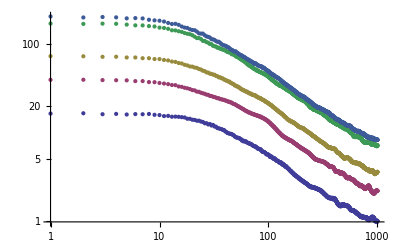

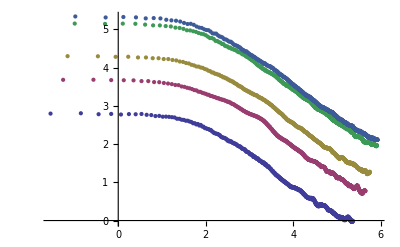

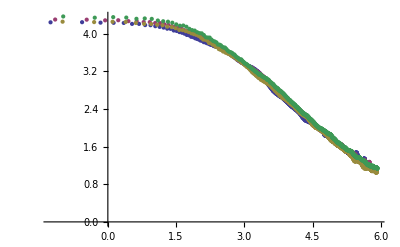

```mathematica
l=10;
d1=0.083;
d2=0.0832;
d3=0.0836;
d4=0.084;
d5=0.0842;
ListLogLogPlot[{frbs[l][d1],frbs[l][d2],frbs[l][d3],frbs[l][d4],frbs[l][d5]},PlotRange->{{1,1000},Full}]
ListPlot[{frbs1[l][d1],frbs1[l][d2],frbs1[l][d3],frbs1[l][d4],frbs1[l][d5]},PlotRange->Full]
pic1=ListPlot[{frbs2[l][d2],frbs2[l][d3],frbs2[l][d4],frbs2[l][d5]},PlotRange->Full]
```

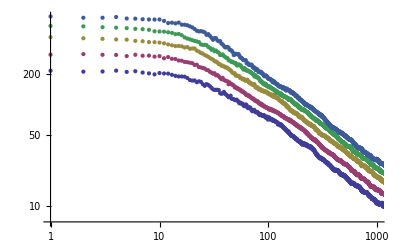

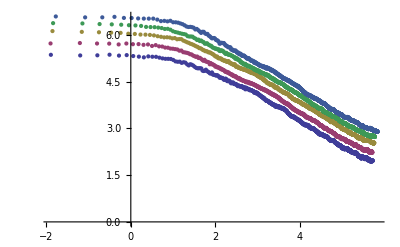

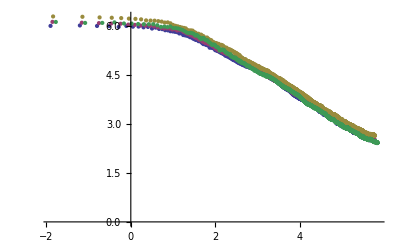

```mathematica
l=20;
d1=0.083;
d2=0.0832;
d3=0.0834;
d4=0.0836;
d5=0.0838;
ListLogLogPlot[{frbs[l][d1],frbs[l][d2],frbs[l][d3],frbs[l][d4],frbs[l][d5]},PlotRange->{{1,1000},Full}]
ListPlot[{frbs1[l][d1],frbs1[l][d2],frbs1[l][d3],frbs1[l][d4],frbs1[l][d5]},PlotRange->Full]
pic2=ListPlot[{frbs2[l][d2],frbs2[l][d3],frbs2[l][d4],frbs2[l][d5]},PlotRange->Full]
```

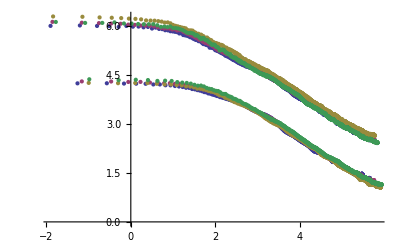

```mathematica
Show[{pic2,pic1}]
```

```mathematica
dif[10][0.0834]
```

-Log[(25 π)/2]+Log[(73 π)/5]

```mathematica
1.+dif[10][0.0834]-1
```

0.155293

```mathematica
d=0.0836;
d0=0.0812;
l=20;
(-d+d0+d1*(l*1000)^(-ω))
```

-0.000520968

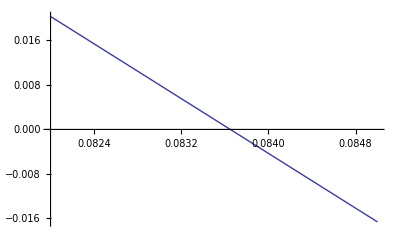

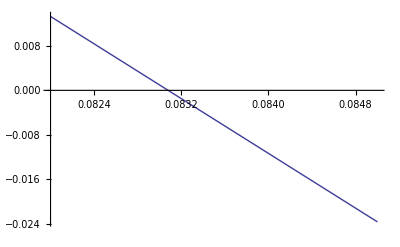

```mathematica
pic3=Plot[(-d+d0+d1*(10*1000)^(-ω))/d0,{d,0.082,0.085}]
pic5=Plot[(-d+d0+d1*(20*1000)^(-ω))/d0,{d,0.082,0.085}]
```

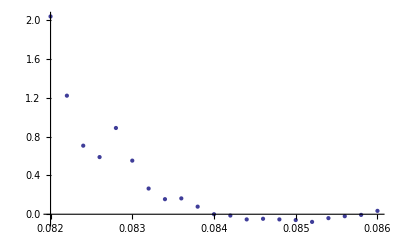

```mathematica
pic4=ListPlot[{dift[10]}]
```

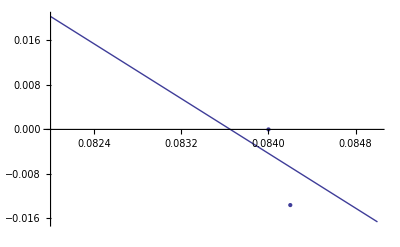

```mathematica
Show[{pic3,pic4}]
```